```mathematica
SetDirectory["/home/dschiebe/Documents/lanayru/PhD_Files/HexaBox_102PureIntsDone"];
PureIntegralsOld=ReadList[FileNameJoin[{Directory[],"files/SortetBasisFull.txt"}]];
PureIntegralsNew=PureIntegralsOld;
Get[FileNameJoin[{Directory[],"HexaBoxModules.m"}]];
PureIntegralsOld[[145]]=PureIntegralsOld[[145]]/.root[x_^2]:>x
$P=2^31-1;
```

-2 (-ep^3+2 ep^4) (mt2 s12-mt2 s123+s123 s345-s12 s45) hxb[0,1,0,1,1,1,0,1,1,0,0,0,0]

# Assemble basis

```mathematica
SelectInts={9,22,75,78,79,80,86,87,88,104,113,131,132,164,165,166,167,168,169}

PureIntegralsNew=PureIntegralsOld;



(*PureIntegralsNew[[153]]=FullSimplify[((mt2 s234-mt2 s34+s16 s34-s234 s345)/((-s234+s34) (-s16+s345)))PureIntegralsNew[[153]]];
PureIntegralsNew[[155]]=FullSimplify[((mt2-s345)/(s16-s345))PureIntegralsNew[[155]]];
PureIntegralsNew[[157]]=FullSimplify[(s123/(s123-s23))PureIntegralsNew[[157]]];*)

PureIntegralsNew[[164]]=FullSimplify[(root[mt2^2-2 mt2 s123+s123^2-2 mt2 s345+2 s123 s345+s345^2-4 s12 s45])PureIntegralsNew[[164]]]
PureIntegralsNew[[165]]=FullSimplify[(s12 root[mt2^2-2 mt2 s123+s123^2-2 mt2 s45-2 s123 s45+s45^2])PureIntegralsNew[[165]]]
PureIntegralsNew[[166]]=FullSimplify[(s12 (s345-s45))PureIntegralsNew[[166]]]
PureIntegralsNew[[167]]=FullSimplify[(mt2 s12-mt2 s123+s123 s345-s12 s45)PureIntegralsNew[[167]]]

PureIntegralsNew[[168]]=((s12-s123) (mt2-s45))PureIntegralsNew[[168]]+((-mt2 (-s12+s123)))PureIntegralsNew[[169]]
PureIntegralsNew[[169]]=root[mt2^4-2 mt2^3 s123+mt2^2 s123^2-2 mt2^3 s345+2 mt2^2 s123 s345+mt2^2 s345^2-2 mt2^3 s45-2 mt2^2 s12 s45+2 mt2^2 s123 s45-2 mt2 s12 s123 s45+4 mt2^2 s345 s45+2 mt2 s12 s345 s45-2 mt2 s123 s345 s45-2 mt2 s345^2 s45+mt2^2 s45^2+2 mt2 s12 s45^2+s12^2 s45^2-2 mt2 s345 s45^2-2 s12 s345 s45^2+s345^2 s45^2]PureIntegralsNew[[169]]

(*PureIntegralsNew[[168]]= ep^3 Expand[hxb[1,0,1,1,0,1,0,1,0,0,0,0,0]*(1/PR[6]-1/PR[8])];
PureIntegralsNew[[169]]= ep^3 Expand[hxb[1,0,1,1,0,1,0,1,0,0,0,0,0]*(1/PR[6]+1/PR[8])];*)

(*PureIntegralsNew[[168]]= ep^2 Expand[hxb[1,0,1,1,0,1,0,1,0,0,0,0,0]*(1/PR[4]1/PR[1])];
PureIntegralsNew[[169]]= ep^2 Expand[hxb[1,0,1,1,0,1,0,1,0,0,0,0,0]*(1/PR[4] 1/PR[3]) ];*)

(*FullSimplify[((s12-s123) (mt2-s45))PureIntegralsNew[[168]]]
PureIntegralsNew[[169]]=FullSimplify[(root[(mt2^4-2 mt2^3 s123+mt2^2 s123^2-2 mt2^3 s345+2 mt2^2 s123 s345+mt2^2 s345^2-2 mt2^3 s45-2 mt2^2 s12 s45+2 mt2^2 s123 s45-2 mt2 s12 s123 s45+4 mt2^2 s345 s45+2 mt2 s12 s345 s45-2 mt2 s123 s345 s45-2 mt2 s345^2 s45+mt2^2 s45^2+2 mt2 s12 s45^2+s12^2 s45^2-2 mt2 s345 s45^2-2 s12 s345 s45^2+s345^2 s45^2)])PureIntegralsNew[[169]]]
*)

SubPureInts=PureIntegralsNew[[SelectInts]];

Newsqrts=(Cases[SubPureInts,root[___],Infinity]//DeleteDuplicates)/.root[x_]:>x
Oldsqrts=(Cases[PureIntegralsOld,root[___],Infinity]//DeleteDuplicates)/.root[x_]:>x
sqrtSetNew=Join[Oldsqrts,Newsqrts]//DeleteDuplicates;
Export[FileNameJoin[{Directory[],"files/Roots.txt"}],sqrtSetNew];

Export[FileNameJoin[{NotebookDirectory[],"SubBasis.txt"}],SubPureInts];
```

{9,22,75,78,79,80,86,87,88,104,113,131,132,164,165,166,167,168,169}

ep^4 hxb[1,0,1,1,0,1,0,1,0,0,0,0,0] root[(-mt2+s123+s345)^2-4 s12 s45]

ep^3 s12 hxb[2,0,1,1,0,1,0,1,0,0,0,0,0] root[mt2^2+(s123-s45)^2-2 mt2 (s123+s45)]

ep^3 s12 (s345-s45) hxb[1,0,2,1,0,1,0,1,0,0,0,0,0]

ep^3 (mt2 (s12-s123)+s123 s345-s12 s45) hxb[1,0,1,2,0,1,0,1,0,0,0,0,0]

-ep^3 mt2 (-s12+s123) hxb[1,0,1,1,0,1,0,2,0,0,0,0,0]+ep^3 (s12-s123) (mt2-s45) hxb[1,0,1,1,0,2,0,1,0,0,0,0,0]

ep^3 hxb[1,0,1,1,0,1,0,2,0,0,0,0,0] root[mt2^4-2 mt2^3 s123+mt2^2 s123^2-2 mt2^3 s345+2 mt2^2 s123 s345+mt2^2 s345^2-2 mt2^3 s45-2 mt2^2 s12 s45+2 mt2^2 s123 s45-2 mt2 s12 s123 s45+4 mt2^2 s345 s45+2 mt2 s12 s345 s45-2 mt2 s123 s345 s45-2 mt2 s345^2 s45+mt2^2 s45^2+2 mt2 s12 s45^2+s12^2 s45^2-2 mt2 s345 s45^2-2 s12 s345 s45^2+s345^2 s45^2]

{-4 mt2 s12+(-mt2-s12+s345)^2,s345^2-2 s345 s45+s45^2,mt2^2-2 mt2 s123+s123^2-2 mt2 s45-2 s123 s45+s45^2,(-mt2+s123+s345)^2-4 s12 s45,mt2^2+(s123-s45)^2-2 mt2 (s123+s45),mt2^4-2 mt2^3 s123+mt2^2 s123^2-2 mt2^3 s345+2 mt2^2 s123 s345+mt2^2 s345^2-2 mt2^3 s45-2 mt2^2 s12 s45+2 mt2^2 s123 s45-2 mt2 s12 s123 s45+4 mt2^2 s345 s45+2 mt2 s12 s345 s45-2 mt2 s123 s345 s45-2 mt2 s345^2 s45+mt2^2 s45^2+2 mt2 s12 s45^2+s12^2 s45^2-2 mt2 s345 s45^2-2 s12 s345 s45^2+s345^2 s45^2}

{(-s12+s34)^2-2 (s12+s34) s56+s56^2,-4 s12 s23 s34 (-s123+s23-s234+s56)+(-s12 s23+s12 s234-s123 s234+s123 s34-s23 s34+s23 s56)^2,-4 mt2 s12+(-mt2-s12+s345)^2,-4 mt2 s56+s56^2,mt2^2-2 mt2 s123+s123^2-2 mt2 s45-2 s123 s45+s45^2,mt2^2-2 mt2 s34+s34^2-2 mt2 s345-2 s34 s345+s345^2,-4 mt2 s12 s34 s56+mt2^2 s56^2-2 mt2 s345 s56^2+s345^2 s56^2,s12^2 s23^2-2 s12^2 s23 s234+2 s12 s123 s23 s234+s12^2 s234^2-2 s12 s123 s234^2+s123^2 s234^2+2 s12 s123 s23 s34-2 s12 s23^2 s34+2 s12 s123 s234 s34-2 s123^2 s234 s34+2 s12 s23 s234 s34+2 s123 s23 s234 s34+s123^2 s34^2-2 s123 s23 s34^2+s23^2 s34^2-2 s12 s23^2 s56+2 s12 s23 s234 s56-2 s123 s23 s234 s56-4 s12 s23 s34 s56+2 s123 s23 s34 s56-2 s23^2 s34 s56+s23^2 s56^2,s345^2-2 s345 s45+s45^2,mt2^2-2 mt2 s16+s16^2-2 mt2 s234-2 s16 s234+s234^2,s16^2-2 s16 s23+s23^2-2 s16 s45-2 s23 s45+s45^2,s56 (-4 mt2 s12 s34+(mt2-s345)^2 s56),s56 (-4 mt2 s12 s34+mt2^2 s56-2 mt2 s345 s56+s345^2 s56)}

```mathematica
PureIntegralsNew[[164]]
PureIntegralsNew[[165]]
PureIntegralsNew[[166]]
PureIntegralsNew[[167]]
PureIntegralsNew[[168]]
PureIntegralsNew[[169]]
```

ep^4 hxb[1,0,1,1,0,1,0,1,0,0,0,0,0] root[(-mt2+s123+s345)^2-4 s12 s45]

ep^3 s12 hxb[2,0,1,1,0,1,0,1,0,0,0,0,0] root[mt2^2+(s123-s45)^2-2 mt2 (s123+s45)]

ep^3 s12 (s345-s45) hxb[1,0,2,1,0,1,0,1,0,0,0,0,0]

ep^3 (mt2 (s12-s123)+s123 s345-s12 s45) hxb[1,0,1,2,0,1,0,1,0,0,0,0,0]

ep^3 (-hxb[1,0,1,1,0,1,0,2,0,0,0,0,0]+hxb[1,0,1,1,0,2,0,1,0,0,0,0,0])

ep^3 (hxb[1,0,1,1,0,1,0,2,0,0,0,0,0]+hxb[1,0,1,1,0,2,0,1,0,0,0,0,0])

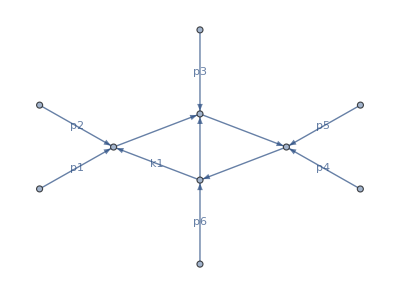

```mathematica
plotDiagram[hxb[1,0,1,1,0,1,0,2,0,0,0,0,0]]
```

```mathematica
mt2^2-2 mt2 s123+s123^2-2 mt2 s345+2 s123 s345+s345^2-4 s12 s45//FullSimplify
```

(-mt2+s123+s345)^2-4 s12 s45

```mathematica
(mt2 s12-mt2 s123+s123 s345-s12 s45)^2//Expand
```

mt2^2 s12^2-2 mt2^2 s12 s123+mt2^2 s123^2+2 mt2 s12 s123 s345-2 mt2 s123^2 s345+s123^2 s345^2-2 mt2 s12^2 s45+2 mt2 s12 s123 s45-2 s12 s123 s345 s45+s12^2 s45^2

{(-s12+s34)^2-2 (s12+s34) s56+s56^2,-4 s12 s23 s34 (-s123+s23-s234+s56)+(-s12 s23+s12 s234-s123 s234+s123 s34-s23 s34+s23 s56)^2,-4 mt2 s12+(-mt2-s12+s345)^2,-4 mt2 s56+s56^2,mt2^2-2 mt2 s123+s123^2-2 mt2 s45-2 s123 s45+s45^2,mt2^2-2 mt2 s34+s34^2-2 mt2 s345-2 s34 s345+s345^2,-4 mt2 s12 s34 s56+mt2^2 s56^2-2 mt2 s345 s56^2+s345^2 s56^2,s12^2 s23^2-2 s12^2 s23 s234+2 s12 s123 s23 s234+s12^2 s234^2-2 s12 s123 s234^2+s123^2 s234^2+2 s12 s123 s23 s34-2 s12 s23^2 s34+2 s12 s123 s234 s34-2 s123^2 s234 s34+2 s12 s23 s234 s34+2 s123 s23 s234 s34+s123^2 s34^2-2 s123 s23 s34^2+s23^2 s34^2-2 s12 s23^2 s56+2 s12 s23 s234 s56-2 s123 s23 s234 s56-4 s12 s23 s34 s56+2 s123 s23 s34 s56-2 s23^2 s34 s56+s23^2 s56^2,s345^2-2 s345 s45+s45^2,mt2^2-2 mt2 s16+s16^2-2 mt2 s234-2 s16 s234+s234^2,s16^2-2 s16 s23+s23^2-2 s16 s45-2 s23 s45+s45^2,s56 (-4 mt2 s12 s34+(mt2-s345)^2 s56),s56 (-4 mt2 s12 s34+mt2^2 s56-2 mt2 s345 s56+s345^2 s56),(mt2 s12-mt2 s123+s123 s345-s12 s45)^2}

# FIX 145!!!

```mathematica
Position[PureIntegralsOld,(mt2 s12-mt2 s123+s123 s345-s12 s45)^2]
```

{{145,4,1}}

```mathematica
PureIntegralsOld[[145]]
```

-2 (-ep^3+2 ep^4) hxb[0,1,0,1,1,1,0,1,1,0,0,0,0] root[(mt2 s12-mt2 s123+s123 s345-s12 s45)^2]

```mathematica
A={{0,a},{b,0}}
```

{{0,a},{b,0}}

{{a b,0},{0,a b}}

```mathematica
UMAT={{1,0},{0,r1}}
```

{{1,0},{0,r1}}

```mathematica
TESTMAT={{a,b},{c,d}}
```

{{a,b},{c,d}}

```mathematica
UMAT.TESTMAT.Inverse[UMAT]
```

{{a,b/r1},{c r1,d}}

```mathematica
PureIntegralsOld[[169]]
PureIntegralsOld[[168]]
```

ep^3 hxb[1,0,1,1,0,1,0,2,0,0,0,0,0]

ep^3 hxb[1,0,1,1,0,2,0,1,0,0,0,0,0]

hxb[1,0,1,0,1,0,1,0,1,0,0,0,0] (ep^3 root[(-s12+s34)^2-2 (s12+s34) s56+s56^2]-2 ep^4 root[(-s12+s34)^2-2 (s12+s34) s56+s56^2])

hxb[1,1,1,1,0,0,1,1,1,0,0,0,0]

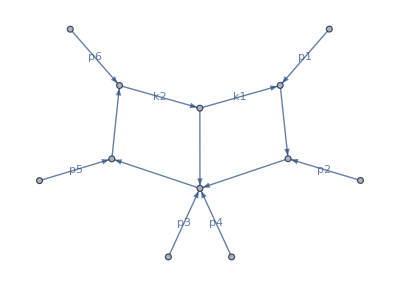

/home/dschiebe/Documents/Diagrams/210.pdf

```mathematica
pos=210;
PureIntegralsNew[[pos]];
INTS=Total[(Cases[PureIntegralsNew[[pos]],_hxb,Infinity]/.{n_Integer:>0/;n<0}//DeleteDuplicates)/.{hxb->List},{1}]/.n_Integer:>1/;n>0/.List->hxb
diagram=plotDiagram[ INTS]
Export[ToString[StringForm["/home/dschiebe/Documents/Diagrams/``.pdf",pos]],diagram]
```

```mathematica
IntList={}
TxtList={}
```

{}

{}

```mathematica
For[i=75,i<=241,i++,
pos=i;
PureIntegralsNew[[pos]];
INTS=Total[(Cases[PureIntegralsNew[[pos]],_hxb,Infinity]/.{n_Integer:>0/;n<0}//DeleteDuplicates)/.{hxb->List},{1}]/.n_Integer:>1/;n>0/.List->hxb;
IntList=Join[IntList,{INTS}];
sectorString=StringForm["``",ToString[StringJoin[Table[ToString[(INTS/.hxb->List)[[q]]],{q,1,Length[INTS/.hxb->List]}]]]];
TxtList=Join[TxtList,{sectorString}];
diagram=plotDiagram[ INTS];
Export[ToString[StringForm["/home/dschiebe/Documents/Diagrams/``.pdf",pos]],diagram];
]
```

```mathematica
IntList//Tally;
```

```mathematica
TxtList//Tally
```

{{1001000100000,1},{0101000100000,2},{0011000100000,2},{1010000100000,1},{1001100100000,2},{0101100100000,1},{0011000110000,1},{1010100100000,1},{1011000100000,3},{0101100110000,2},{1101100100000,2},{1010100110000,1},{1011100100000,1},{0111000110000,2},{1111000100000,2},{1111100100000,1},{1111100110000,3},{1010001110000,1},{1010010100000,1},{1010010110000,1},{1010011110000,1},{1010101100000,1},{1010101110000,1},{1010110110000,1},{1010111100000,1},{1010111110000,1},{0011001100000,1},{0011010100000,1},{0101001100000,1},{1001001100000,1},{0101001110000,2},{1101001100000,2},{0011001110000,2},{0011010110000,2},{0101010100000,2},{0101101100000,2},{0011011100000,1},{0101011100000,1},{0101110100000,1},{1001010100000,2},{1001011100000,1},{1001101100000,2},{1001110100000,1},{0101010110000,2},{0011011110000,2},{0101011110000,2},{0101101110000,2},{0101110110000,2},{0101111100000,2},{1001111100000,2},{0101111110000,1},{0111001100000,2},{0111010100000,2},{1101010100000,2},{1011001100000,6},{1011010100000,6},{1011001110000,1},{1011010110000,1},{1011101100000,1},{1011110100000,1},{0111001110000,2},{0111010110000,2},{0111011100000,2},{1101011100000,2},{1101101100000,2},{1101110100000,2},{1111001100000,5},{1011011100000,6},{1111010100000,6},{0111011110000,1},{1011011110000,1},{1011111100000,1},{1101111100000,1},{1111110100000,3},{1111001110000,4},{1111010110000,4},{1111101100000,4},{1111011100000,7},{1111011110000,3},{1111101110000,3},{1111110110000,3},{1111111100000,3},{1111111110000,1}}